### Gradient Descent Algorithm

```mathematica
1
```

```mathematica
SeedRandom[888]
x=RandomReal[{0,1},50];
y=-1-x+0.6*RandomReal[{0,1},50];
```

```mathematica
2
```

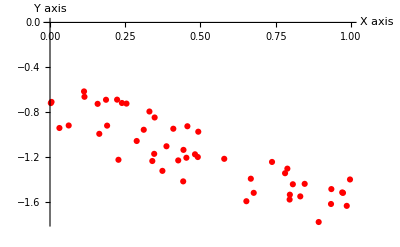

```mathematica
ListPlot[Transpose[{x,y}],AxesLabel->{"X axis","Y axis"},PlotStyle->Red]
```

```mathematica
3
```

```mathematica
itt=250;(*Number of iterations*)
α=0.0001;(*Learning rate*)
θ0=Range@@{0,itt};(* Array for values of Theta_0*)
θ1=Range@@{0,itt};(* Array for values of Theta_1*)
Table[{θ0⟦i+1⟧=θ0⟦i⟧-α/(Length@x)*Sum[(θ0⟦i⟧+θ1⟦i⟧* x⟦j⟧-y⟦j⟧),{j,1,Length@x}];
θ1⟦i+1⟧=θ1⟦i⟧-α/(Length@x)*Sum[( θ0⟦i⟧+θ1⟦i⟧*x⟦j⟧- y⟦j⟧)*x⟦j⟧,{j,1,Length@x}];},{i,1,itt}];
```

```mathematica
4
```

```mathematica
F[X_]:=θ0⟦Length@θ0⟧+θ1⟦Length@θ1⟧*X
```

```mathematica
5
```

```mathematica
F[X]
```

-0.707789-0.923729 X

```mathematica
6
```

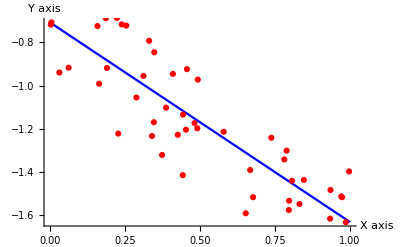

```mathematica
Show[{Plot[F[X],{X,0,1},PlotStyle->Blue,AxesLabel->{"X axis","Y axis"}],ListPlot[Transpose[{x,y}],PlotStyle->Red]}]
```

```mathematica
7
```

```mathematica
J[Theta0_,Theta1_]:=1/(2*Length[x])*Sum[ (Theta0+(Theta1*x[[i]])- y[[i]])^2,{i,1,Length@x}]
```

```mathematica
8
```

```mathematica
α1=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α2=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α3=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α4=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
α5=Transpose[{Range[0,itt],J[θ0,θ1]}];
```

```mathematica
9
```

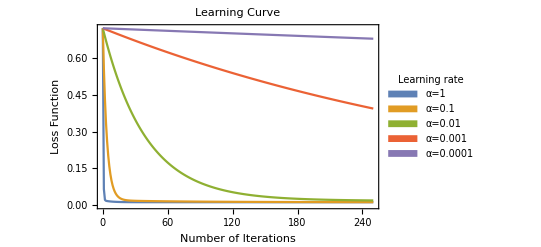

```mathematica
ListLinePlot[{α1,α2,α3,α4,α5},FrameLabel->{"Number of Iterations","Loss Function"},Frame->True,PlotLabel->"Learning Curve",PlotLegends->SwatchLegend[{Style["α=1",#],Style["α=0.1",#],Style["α=0.01",#],Style["α=0.001",#],Style["α=0.0001",#]},LegendLabel->Style["Learning rate",White],LegendFunction->(Framed[#,RoundingRadius->5,Background->Gray]&)]]&[White]
```

### Linear Regression

```mathematica
1
```

```mathematica
Bstn=ResourceData[ResourceObject["Sample Data: Boston Homes"]]
```

```mathematica
2
```

```mathematica
ResourceData[ResourceObject["Sample Data: Boston Homes"],"ColumnDescriptions"]//TableForm
```

Per capita crime rate by town
Proportion of residential land zoned for lots over 25000 square feet
Proportion of non-retail business acres per town
Charles River dummy variable (1 if tract bounds river, 0 otherwise)
Nitrogen oxide concentration (parts per 10 million)
Average number of rooms per dwelling
Proportion of owner-occupied units built prior to 1940
Weighted mean of distances to five Boston employment centers
Index of accessibility to radial highways
Full-value property-tax rater per $10000
Pupil-teacher ratio by town
1000(Bk-0.63)^2 where Bk is the proportion of Black or African-American residents by town
Lower status of the population (percent)
Median value of owner-occupied homes in $1000s

```mathematica
3
```

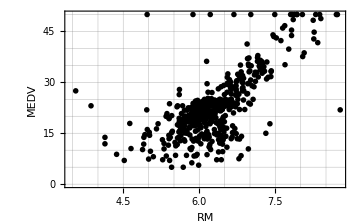

```mathematica
MEDVvsRM=Transpose[{Normal[Bstn[All,"RM"]],Normal[Bstn[All,"MEDV"]]}];
ListPlot[MEDVvsRM,PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{Style["RM",Red],Style["MEDV",Red]},GridLines->All,PlotStyle->Black,ImageSize->Medium]
```

```mathematica
4
```

```mathematica
CorreLat=SetPrecision[Correlation[Transpose[{Normal[Bstn[All,"RM"]],Normal[Bstn[All,"MEDV"]]}]],2];
XTicks={{1,"RM"},{2,"MEDV"},{1,"RM"},{2,"MEDV"}};
YTicks={{1,"RM"},{2,"MEDV"},{1,"RM"},{2,"MEDV"}};
PostionsValues={Text[#1,{0.5,1.5}],Text[#1,{1.5,0.5}],Text[#2,{1.5,1.5}],Text[#2,{0.5,0.5}]}&[CorreLat⟦1,1⟧,CorreLat⟦1,2⟧];
MatrixPlot[CorreLat,ColorFunction->"DarkRainbow",FrameTicks->{  XTicks,YTicks,XTicks,YTicks},Epilog->{White,PostionsValues},PlotLegends->BarLegend[{"DarkRainbow",{0,1}},4],ImageSize->180]
```

-Graphics-

```mathematica
5
```

```mathematica
NewData=RandomSample[Thread[Normal[Bstn[All,"RM"]]->Normal[Bstn[All,"MEDV"]]]];
```

```mathematica
6
```

```mathematica
{training,test}={NewData⟦;;354⟧,NewData⟦355;;⟧};
```

```mathematica
7
```

```mathematica
PF=Predict[training,Method->"LinearRegression",TrainingProgressReporting->"Panel"]
```

PredictorFunction[…]

```mathematica
8
```

```mathematica
Information[PF]
```

Predictor information
Data type | Numerical
Standard deviation | 6.39 ± 0.55
Method | LinearRegression
Single evaluation time | 3.12 ms/example
Batch evaluation speed | 86.9 examples/ms
Loss | 3.27 ± 0.094
Model memory | 219. kB
Training examples used | 354 examples
Training time | 2.29 s
 |

```mathematica
9
```

```mathematica
PRM=PredictorMeasurements[PF,test]
```

PredictorMeasurementsObject[…]

```mathematica
10
```

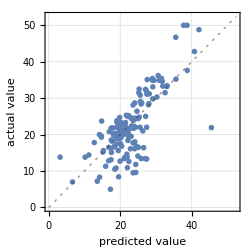
Predictor Measurements
Number of test examples | 152
Standard deviation | 5.73 ± 0.45
Standard deviation baseline | 8.44 ± 0.61
Mean cross entropy | 3.2 ± 0.052
Single evaluation time | 3.37 ms/example
Batch evaluation speed | 146. examples/s
-Graphics- |

```mathematica
PRM["Report"]
```

```mathematica
11
```

```mathematica
Dataset[AssociationMap[PRM[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared"}]]
```

```mathematica
12
```

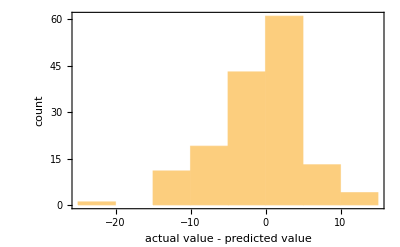
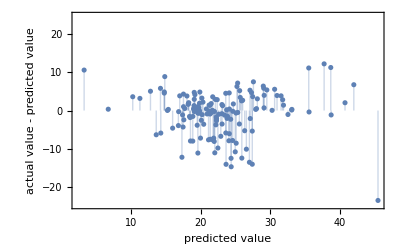
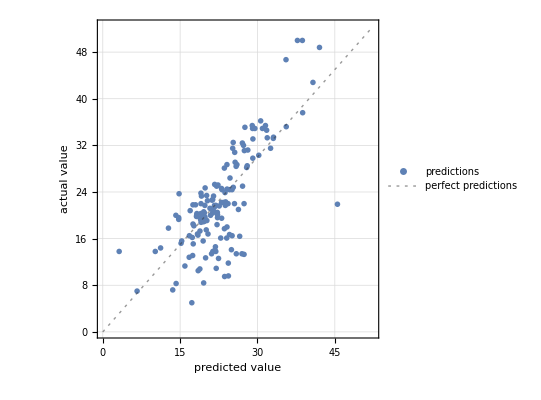

```mathematica
PRM[#]&/@{"ResidualHistogram","ResidualPlot","ComparisonPlot"}
```

```mathematica
13
```

```mathematica
PRM["Properties"]
```

{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,FractionVarianceUnexplained,GeometricMeanProbabilityDensity,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,RSquared,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples}

```mathematica
14
```

```mathematica
Information[PF,"MethodOption"]
```

Method→{LinearRegression,L1Regularization→0,L2Regularization→0.00001,OptimizationMethod→NormalEquation}

```mathematica
15
```

```mathematica
PF2=Predict[training,Method->{"LinearRegression","L1Regularization"-> 12,"L2Regularization"->100,"OptimizationMethod"-> Automatic},TrainingProgressReporting->None,PerformanceGoal->"Quality",RandomSeeding->10000,TargetDevice->"CPU"];
```

```mathematica
16
```

```mathematica
PRM2=PredictorMeasurements[PF2,test];
PRM[#]&/@{"ResidualHistogram","ResidualPlot","ComparisonPlot"}
Dataset[AssociationMap[PRM2[#,ComputeUncertainty->True]&,{"StandardDeviation","RSquared"}]]
```

{-Graphics-,-Graphics-,-Graphics-}

### Logistic Regression

```mathematica
1
```

```mathematica
Titanic=Query[AssociationThread[Range[Length@#]->Range[Length@#]]][ExampleData[{"Dataset","Titanic"}]]&[ExampleData[{"Dataset","Titanic"}]]
```

```mathematica
2
```

```mathematica
Dimensions@Titanic
```

{1309,4}

```mathematica
3
```

```mathematica
Query[Count[_Missing],#]@Titanic&/@{"class","age","sex","survived"}
```

{0,263,0,0}

```mathematica
4
```

```mathematica
Query[Select[#age==Missing[]&]][Titanic];
Normal@Keys@%
```

{16,38,41,47,60,70,71,75,81,107,108,109,119,122,126,135,148,153,158,167,177,180,185,197,205,220,224,236,238,242,255,257,270,278,284,294,298,319,321,364,383,385,411,470,474,478,484,492,496,525,529,532,582,596,598,673,681,682,683,706,707,757,758,768,769,776,790,796,799,801,802,803,805,806,809,813,814,816,817,820,836,843,844,853,855,857,859,866,872,873,875,877,880,883,887,888,901,902,903,904,919,921,922,923,924,927,928,929,930,931,932,941,943,945,946,947,949,955,956,957,958,959,962,963,972,974,977,983,984,985,988,989,990,992,994,995,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1010,1013,1014,1015,1017,1019,1023,1024,1028,1029,1030,1031,1033,1034,1035,1036,1037,1038,1039,1040,1042,1043,1044,1045,1053,1054,1055,1056,1070,1071,1072,1073,1074,1075,1077,1078,1079,1081,1082,1086,1096,1110,1115,1116,1117,1122,1123,1124,1125,1129,1133,1136,1137,1138,1139,1150,1151,1152,1155,1156,1160,1163,1164,1165,1167,1168,1169,1171,1173,1174,1175,1176,1177,1178,1179,1180,1181,1185,1186,1187,1194,1195,1196,1198,1199,1200,1201,1203,1213,1214,1215,1216,1217,1220,1222,1242,1243,1244,1246,1247,1248,1250,1251,1254,1256,1263,1269,1283,1284,1285,1292,1293,1294,1298,1303,1304,1306}

```mathematica
5
```

```mathematica
Titanic=DeleteMissing[Titanic,1,1]
```

```mathematica
6
```

```mathematica
Titanic[Key[16]]
```

Missing[KeyAbsent,16]

```mathematica
7
```

```mathematica
Dataset@
<|
"Class"->Query[Counts,"class"]@Titanic,"Sex"-> Query[Counts,"sex"]@Titanic,
"Survival status"->Query[Counts,"survived"]@Titanic
|>
```

```mathematica
8
```

```mathematica
Row[{PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#))}&[Counts[Query[All,"survived"][Titanic]]], PlotLabel->Style["Percentage of survival",#3,#4], ChartLegends-> {"Survived", "Died"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)],
PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#))}&[Counts[Query[All,"sex"][Titanic]]], PlotLabel->Style["Percentage by sex",#3,#4], ChartLegends->{"Female", "Male"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)],
PieChart[{N@((#[[1]])/(Total@#)),N@((#[[2]])/(Total@#)),N@((#[[3]])/(Total@#))}&[Counts[Query[All,"class"][Titanic]]], PlotLabel->Style["Percentage by class",#3,#4], ChartLegends->{"1st", "2nd","3rd"}, ImageSize->#1,ChartStyle->#2,LabelingFunction->(Placed[Row[{SetPrecision[100#,3],"%"}],"RadialCallout"]&)]},"----"]&[200,{ColorData[97,20],ColorData[97,13],ColorData[97,32]},Black,20]
```

---------Graphics--Graphics--Graphics-

```mathematica
9
```

```mathematica
BlockRandom[SeedRandom[8888];
RandomSample[Titanic]];
Keys@Normal@Query[All][%];
{train,test}={%[[1;;837]],%[[838;;1046]]};
dataset=Query[<|"Train"->{Map[Key,train]},"Test"->{Map[Key,test]} |> ][Titanic]
```

```mathematica
10
```

```mathematica
CF=Classify[Flatten[Values[Normal[Query["Train",All,All,{#class,#age,#sex}-> #survived&][dataset]]]],Method->{"LogisticRegression","L1Regularization"-> Automatic,"L2Regularization"-> Automatic,"OptimizationMethod"->"StochasticGradientDescent"},PerformanceGoal->"Quality",RandomSeeding->100000,TargetDevice->"CPU",TrainingProgressReporting->None]
```

ClassifierFunction[…]

```mathematica
11
```

```mathematica
Information[CF]
```

Classifier information
Data type | {Nominal,Numerical,Nominal}
Classes | ,,FalseTrue
Accuracy | (79.12.0) %
Method | LogisticRegression
Single evaluation time | 4.04 ms/example
Batch evaluation speed | 35.7 examples/ms
Loss | 0.498 ± 0.027
Model memory | 350. kB
Training examples used | 837 examples
Training time | 12.8 s
 |

```mathematica
12
```

```mathematica
Information[CF,"Properties"]
```

{Accuracy,BatchEvaluationSpeed,BatchEvaluationTime,Classes,ClassNumber,ClassPriors,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,OptimizationMethod,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
13
```

```mathematica
CF[{"3rd",23,"male"},{"Probability"-> False,"TopProbabilities"-> 2}]
```

{0.839494,{False→0.839494,True→0.160506}}

```mathematica
14
```

```mathematica
Dataset@
AssociationMap[CF[{"3rd",23,"male"},#]
&,{"Decision","Distribution","ExpectedUtilities","LogProbabilities","Probabilities","TopProbabilities"}]
```

```mathematica
15
```

```mathematica
CM=ClassifierMeasurements[CF,Flatten[Values[Normal[Query["Test",All,All,{#class,#age,#sex}-> #survived&][dataset]]]],ComputeUncertainty->True,RandomSeeding->8888]
```

ClassifierMeasurementsObject[…]

```mathematica
16
```

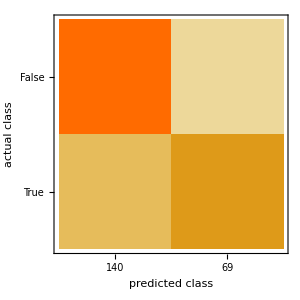
Classifier Measurements
Number of test examples | 209
Accuracy | (73.73.1) %
Accuracy baseline | (60.83.4) %
Geometric mean of probabilities | 0.572 ± 0.022
Mean cross entropy | 0.558 ± 0.039
Single evaluation time | 6.77 ms/example
Batch evaluation speed | 14.9 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
CM["Report"]
```

```mathematica
17
```

```mathematica
CM["ConfusionMatrixPlot"]
```

-Graphics-

```mathematica
18
```

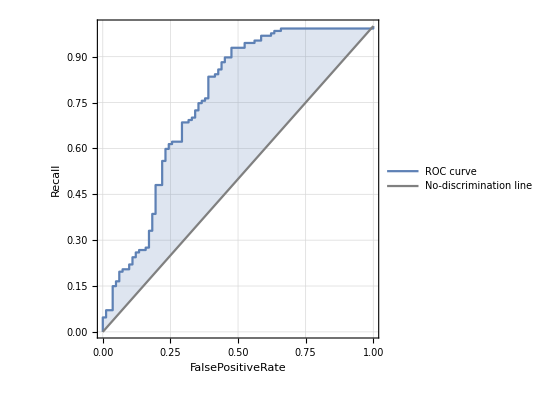
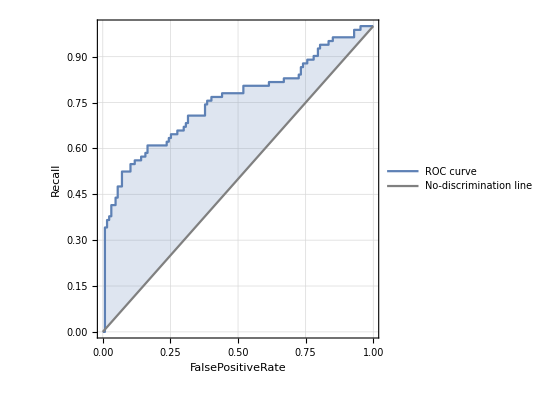
{<|False→-Graphics-,True→-Graphics-|>,}

```mathematica
{CM["ROCCurve"],Dataset@<|{"AUC"->CM["AreaUnderROCCurve"]},{"MCC"->CM["MatthewsCorrelationCoefficient"]}|>}
```

```mathematica
19
```

```mathematica
CM[{"LeastCertainExamples","ClassMeanCrossEntropy"}]
```

{{{3rd,39,female}→False,{3rd,38,female}→True,{3rd,37,female}→False,{3rd,37,female}→False,{3rd,36,female}→True,{3rd,32,female}→False,{1st,4,male}→True,{3rd,30,female}→False,{3rd,28,female}→False,{3rd,27,female}→True},<|False→0.363541,True→0.85931|>}

```mathematica
20
```

```mathematica
CM[#]&/@{"FalseDiscoveryRate","FalseNegativeRate","FalsePositiveRate"}
```

{<|False→0.242857,True→0.304348|>,<|False→0.165354,True→0.414634|>,<|False→0.414634,True→0.165354|>}

```mathematica
21
```

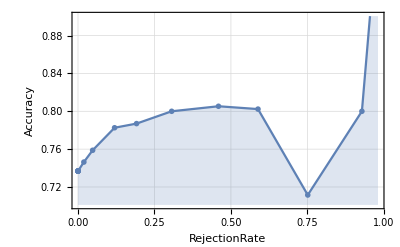
0.736842
<|False→0.834646,True→0.585366|>
<|False→0.794007,True→0.635762|>
<|False→0.757143,True→0.695652|>
-Graphics-

```mathematica
CM[{"Accuracy","Recall","F1Score","Precision","AccuracyRejectionPlot"}]//TableForm
```

```mathematica
22
```

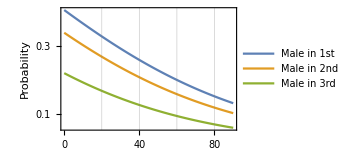
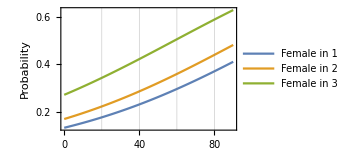
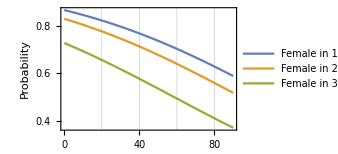
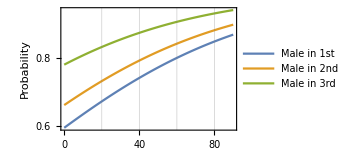
True class | False class
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TruPlot={Plot[{CF[{#1,age,#4},"Probability"-> #6 ],CF[{#2,age,#4},"Probability"-> #6 ],CF[{#3,age,#4},"Probability"-> #6 ]}, {age,0,90},PlotLegends->{"Male in 1st class", "Male in 2nd class ", "Male in 3rd class"},FrameLabel-> {Style["Age in years",Bold,15], Style["Probability",Bold,15]}, Frame->#6,FrameTicks->#7,GridLines-> {{20,40,60,80}},ImageSize->#8],Plot[{CF[{#1,age,#5},"Probability"-> #6 ],CF[{#2,age,#5},"Probability"-> #6 ],CF[{#3,age,#5},"Probability"-> #6 ]}, {age,0,90},PlotLegends->{"Female in 1st class", "Female in 2nd class ", "Female in 3rd class"},FrameLabel-> {Style["Age in years",Bold,15], Style["Probability",Bold,15]}, Frame->#6,FrameTicks->#7,GridLines-> {{20,40,60,80}},ImageSize->#8]}&["1st","2nd","3rd","male","female",True,All,250];
FalsPlot={Plot[{CF[{#1,age,#4},"Probability"-> #6 ],CF[{#2,age,#4},"Probability"-> #6],CF[{#3,age,#4},"Probability"-> #6]}, {age,0,90},PlotLegends->{"Male in 1st class", "Male in 2nd class ", "Male in 3rd class"},FrameLabel-> {Style["Age in years",Bold,15], Style["Probability",Bold,15]}, Frame->True,FrameTicks->#7,GridLines-> {{20,40,60,80}},ImageSize->#8],Plot[{CF[{#1,age,#5},"Probability"-> #6 ],CF[{#2,age,#5},"Probability"-> #6 ],CF[{#3,age,#5},"Probability"-> #6]}, {age,0,90},PlotLegends->{"Female in 1st class", "Female in 2nd class ", "Female in 3rd class"},FrameLabel-> {Style["Age in years",Bold,15], Style["Probability",Bold,15]}, Frame->True,FrameTicks->#7,GridLines-> {{20,40,60,80}},ImageSize->#8]}&["1st","2nd","3rd","male","female",False,All,250];
Headings={Style["True class",Black,20,FontFamily->"Arial Rounded MT"],Style["False class",Black,20,FontFamily->"Arial Rounded MT"]};
Grid[{{Headings[[1]],Headings[[2]]},{TruPlot[[1]],FalsPlot[[2]]},{TruPlot[[2]],FalsPlot[[1]]}},Alignment->{{Center,Center},{None,None}},Dividers->{False,1}]
```

### Data Clustering

```mathematica
1
```

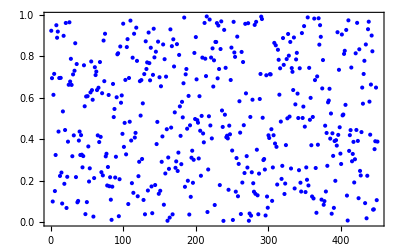

```mathematica
BlockRandom[
SeedRandom[321];
RndPts=Table[{i,RandomReal[{0,1}]},{i,1,450}];]
ListPlot[RndPts,PlotRange->All,PlotStyle->Directive[Thick,Blue],Frame->True,FrameTicks->All]
```

```mathematica
2
```

```mathematica
Clusters=FindClusters[RndPts,PerformanceGoal->"Speed",Method->Automatic,DistanceFunction->Automatic,RandomSeeding->1234];
Short[Clusters,4]
```

{{{1,0.924416},{2,0.695055},{5,0.715785},{8,0.951038},«137»,{372,0.895003},{395,0.917268},{410,0.974659},{422,0.962478}},{«1»},{{236,«19»},«166»}}

```mathematica
3
```

```mathematica
Length[Clusters]
```

3

```mathematica
4
```

```mathematica
Map[Dimensions,Clusters,1]
```

{{145,2},{138,2},{167,2}}

```mathematica
5
```

```mathematica
ListPlot[Clusters,PlotStyle->{Red,Blue,Green},PlotLegends->Automatic,Frame->True,FrameTicks->All,PlotLabel->Style["Cluster Plot",Italic,20,Black],Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}]
```

-Graphics-

```mathematica
6
```

```mathematica
{Cluster1Centroid,Cluster2Centroid,Cluster3Centroid}={N@Mean@Clusters⟦1,All⟧,N@Mean@Clusters⟦2,All⟧,N@Mean@Clusters⟦3,All⟧}
```

{{182.807,0.815713},{115.935,0.300888},{353.108,0.39227}}

```mathematica
7
```

```mathematica
ClusterPlot=ListPlot[Clusters,PlotStyle->{Red,Blue,Green},PlotLegends->{"Cluster 1","Cluster 2","Cluster 3"}];
CentroidPlot=ListPlot[{Cluster1Centroid,Cluster2Centroid,Cluster3Centroid},PlotStyle->Black];
Show[{ClusterPlot,CentroidPlot},Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Frame-> True,FrameTicks-> All,PlotLabel->Style["Cluster Plot",Italic,20,Black]]
```

-Graphics-

```mathematica
8
```

```mathematica
Show[{ClusterPlot,CentroidPlot},Prolog->{LightYellow,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Frame-> True,FrameTicks-> All,Epilog->{Opacity[0.2],PointSize[0.1],Point[Cluster1Centroid],Point[Cluster2Centroid],Point[Cluster3Centroid]}]
```

-Graphics-

```mathematica
9
```

```mathematica
Classes=ClusteringComponents[Clusters,3,2,Method->Automatic,DistanceFunction->Automatic,RandomSeeding-> 1234,PerformanceGoal->"Speed"]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,2,1,2,2,1,1,1,1,2,1,1,2,1,1,2,1,2,2,2,2,1,1,2,2,1,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,3,1,3,1,1,1,1,1,1,1,1,1,3,1,3,3,1,3,1,1,3,1,1,1,1,3,1,3,1,1,1,3,3,1,1,3,3,3,3,3,3},{2,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,2,2,2,3,2,2,3,3,2,3,3,3,2,3,3,3,3,3,2,3,2,3,3,3,3,2,3,3,2,3,3,2,2,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,2,3,3,2,2,3,2,3,3,3,3,3,2,3,3,3,3,3,2,3,3,3,2,3,3,3,2,3,2,2,3,2,3,3,2,2,3,3,2,2,2,3,3,3,3,2,3,3}}

```mathematica
10
```

```mathematica
Flatten[Classes]//Counts
```

<|1→174,2→132,3→144|>

```mathematica
11
```

```mathematica
ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}

```mathematica
12
```

```mathematica
iris=ExampleData[{"Statistics","FisherIris"}];
```

```mathematica
13
```

```mathematica
Short[iris,6]
```

{{5.1,3.5,1.4,0.2,setosa},{4.9,3.,1.4,0.2,setosa},{4.7,3.2,1.3,0.2,setosa},{4.6,3.1,1.5,0.2,setosa},{5.,3.6,1.4,0.2,setosa},{5.4,3.9,1.7,0.4,setosa},{4.6,3.4,1.4,0.3,setosa},{5.,3.4,1.5,0.2,setosa},{4.4,2.9,1.4,0.2,setosa},{4.9,3.1,1.5,0.1,setosa},{5.4,3.7,1.5,0.2,setosa},{4.8,3.4,1.6,0.2,setosa},«126»,{6.,3.,4.8,1.8,virginica},{6.9,3.1,5.4,2.1,virginica},{6.7,3.1,5.6,2.4,virginica},{6.9,3.1,5.1,2.3,virginica},{5.8,2.7,5.1,1.9,virginica},{6.8,3.2,5.9,2.3,virginica},{6.7,3.3,5.7,2.5,virginica},{6.7,3.,5.2,2.3,virginica},{6.3,2.5,5.,1.9,virginica},{6.5,3.,5.2,2.,virginica},{6.2,3.4,5.4,2.3,virginica},{5.9,3.,5.1,1.8,virginica}}

```mathematica
14
```

```mathematica
ST=Standardize[iris[[All,{1,2,3,4}]]];(*Showing only the first 4 terms*)
%[[1;;4]]//TableForm
```

-0.897674 | 1.0156 | -1.33575 | -1.31105
-1.1392 | -0.131539 | -1.33575 | -1.31105
-1.38073 | 0.327318 | -1.3924 | -1.31105
-1.50149 | 0.0978893 | -1.2791 | -1.31105

```mathematica
15
```

```mathematica
DR=DimensionReduction[ST,2,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
16
```

```mathematica
PCA=DR[ST,"ReducedVectors"];
TableForm[%[[1;;5]],TableHeadings->{None, {"First principal component","Second Principal component"}},TableAlignments->Center]
```

First principal component | Second Principal component
-2.2647 | 0.480027
-2.08096 | -0.674134
-2.36423 | -0.341908
-2.29938 | -0.597395
-2.38984 | 0.646835

```mathematica
17
```

```mathematica
(Variance@PCA⟦All,All⟧)/(Total@Variance@PCA⟦All,All⟧)//TableForm[#,TableHeadings->{{"First PC variation","Second PC variation"}, None}]&
```

First PC variation | 0.761507
Second PC variation | 0.238493

```mathematica
18
```

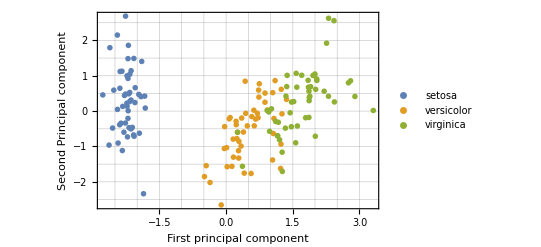

```mathematica
Labels={Style["First principal component",Black,Bold],Style["Second Principal component",Black,Bold]};
ListPlot[{PCA⟦1;;50⟧,PCA⟦51;;100⟧,PCA⟦100;;150⟧},PlotLegends->Placed[{Placeholder["setosa"],Placeholder["versicolor"],Placeholder["virginica"]},Right],PlotMarkers->"OpenMarkers",GridLines->All,Frame->True,Axes->False,FrameTicks->All,FrameLabel->Labels]
```

```mathematica
19
```

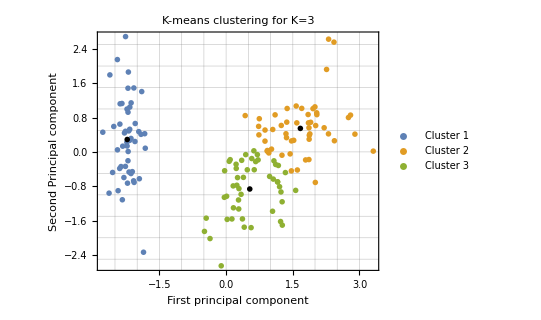

```mathematica
Clstr=FindClusters[PCA,3,Method->"KMeans",DistanceFunction->SquaredEuclideanDistance,RandomSeeding->8888];
ListPlot[Clstr,PlotRange->All,Frame->True,AspectRatio->0.8,Axes->False,PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]},PlotLabel->Style["K-means clustering for K=3",FontFamily->"Times",Black,20,Italic],FrameTicks->All,PlotLegends->Placed[{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]},Right],PlotMarkers-> "OpenMarkers",FrameLabel->Labels,GridLines->All,Epilog->{Opacity[1],PointSize[0.01],Point[Mean@Clstr⟦1,All⟧],Point[Mean@Clstr⟦2,All⟧],Point[Mean@Clstr⟦3,All⟧]}]
```

```mathematica
20
```

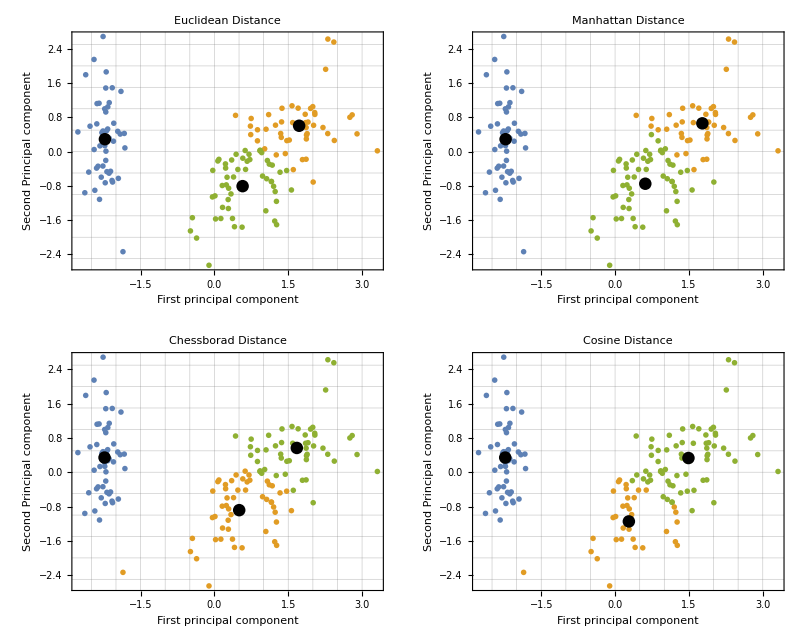
-Graphics-K-means clustering for K=3

```mathematica
{ED,MhD,ChD,CosD}={FindClusters[PCA,3,PerformanceGoal->#1,Method->#2,DistanceFunction->EuclideanDistance,RandomSeeding->#3],FindClusters[PCA,3,PerformanceGoal->#1,Method->#2,DistanceFunction->ManhattanDistance,RandomSeeding->#3],FindClusters[PCA,3,PerformanceGoal->#1,Method->#2,DistanceFunction->ChessboardDistance,RandomSeeding->#3],FindClusters[PCA,3,PerformanceGoal->#1,Method->#2,DistanceFunction->CosineDistance,RandomSeeding->#3]}&["Quality","KMeans",8888];
{EDplt,MhDplt,ChDplt,CosDplt}={
ListPlot[ED,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@ED⟦1,All⟧],Point[Mean@ED⟦2,All⟧],Point[Mean@ED⟦3,All⟧]},PlotLabel-> Style["Euclidean Distance",Black]],
ListPlot[MhD,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@MhD⟦1,All⟧],Point[Mean@MhD⟦2,All⟧],Point[Mean@MhD⟦3,All⟧]},PlotLabel-> Style["Manhattan Distance",Black]],
ListPlot[ChD,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@ChD⟦1,All⟧],Point[Mean@ChD⟦2,All⟧],Point[Mean@ChD⟦3,All⟧]},PlotLabel-> Style["Chessborad Distance",Black]],
ListPlot[CosD,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@CosD⟦1,All⟧],Point[Mean@CosD⟦2,All⟧],Point[Mean@CosD⟦3,All⟧]},PlotLabel-> Style["Cosine Distance",Black]]
}&[True,0.8,"OpenMarkers",{ColorData[97,1],ColorData[97,2],ColorData[97,3]},All,Automatic,300,Labels,False,All,1,0.03];
LegendsText={Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]};
Labeled[Legended[GraphicsGrid[{{EDplt,MhDplt},{ChDplt,CosDplt}},Frame->All,Background->White,Spacings->1],PointLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},LegendsText,LegendMarkers->"OpenMarkers"]],Style["K-means clustering for K=3",FontFamily->"Times",Black,20,Italic],Top]
```

```mathematica
21
```

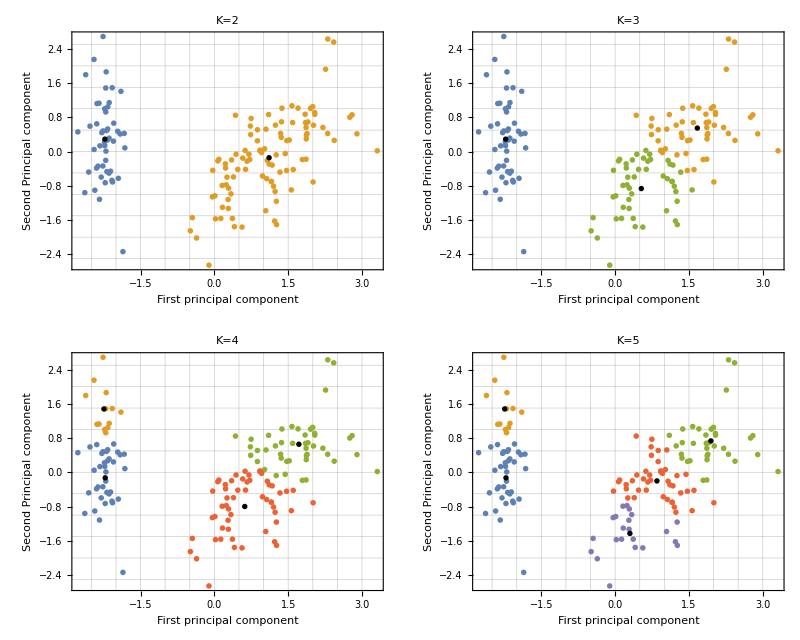
-Graphics-K-means clustering for K=2,3,4,5

```mathematica
{K2,K3,K4,K5}={FindClusters[PCA,2,PerformanceGoal->#1,Method->#2,DistanceFunction->#3,RandomSeeding->#4],FindClusters[PCA,3,PerformanceGoal->#1,Method->#2,DistanceFunction->#3,RandomSeeding->#4],FindClusters[PCA,4,PerformanceGoal->#1,Method->#2,DistanceFunction->#3,RandomSeeding->#4],FindClusters[PCA,5,PerformanceGoal->#1,Method->#2,DistanceFunction->#3,RandomSeeding->#4]}&["Speed","KMeans",SquaredEuclideanDistance,8888];
{PK2,PK3,PK4,PK5}={
ListPlot[K2,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@K2⟦1,All⟧],Point[Mean@K2⟦2,All⟧]},PlotLabel-> Style["K=2",Black]],
ListPlot[K3,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@K3⟦1,All⟧],Point[Mean@K3⟦2,All⟧],Point[Mean@K3⟦3,All⟧]},PlotLabel-> Style["K=3",Black]],
ListPlot[K4,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@K4⟦1,All⟧],Point[Mean@K4⟦2,All⟧],Point[Mean@K4⟦3,All⟧],Point[Mean@K4⟦4,All⟧]},PlotLabel-> Style["K=4",Black]],
ListPlot[K5,Frame->#1,AspectRatio->#2,PlotMarkers->#3,PlotStyle->#4,GridLines->#5,PlotRange->#6,ImageSize->#7,FrameLabel->#8,Axes->#9,FrameTicks->#10,
Epilog->{Opacity@#11,PointSize@#12,Point[Mean@K5⟦1,All⟧],Point[Mean@K5⟦2,All⟧],Point[Mean@K5⟦3,All⟧],Point[Mean@K5⟦4,All⟧],Point[Mean@K5⟦5,All⟧]},PlotLabel-> Style["K=5",Black]]
}&[True,0.8,"OpenMarkers",{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],ColorData[97,5]},All,Automatic,260,Labels,False,All,1,0.015];
LegendsText2={Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]],Placeholder[Style["Cluster 4",Bold,Black,10]],Placeholder[Style["Cluster 5",Bold,Black,10]]};
Labeled[Legended[GraphicsGrid[{{PK2,PK3},{PK4,PK5}},Frame->All,Background->White,Spacings->1],PointLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],ColorData[97,5]},LegendsText2,LegendMarkers->"OpenMarkers"]],Style["K-means clustering for K=2,3,4,5",FontFamily->"Times",Black,20,Italic],Top]
```

```mathematica
22
```

```mathematica
ClusteringComponents[Clstr,3,2,Method->"KMeans",DistanceFunction->SquaredEuclideanDistance,RandomSeeding->8888]
```

{{1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{2,3,2,2,2,2,3,2,3,2,3,2,3,2,3,3,3,3,3,2,2,2,2,3,2,3,2,2,2,3,2,2,2,2,2,3,2,2,3,2,3,3,3,3,3,3,3,3,3}}

```mathematica
23
```

```mathematica
Counts[Flatten[%]]
```

<|1→46,2→29,3→75|>

```mathematica
24
```

```mathematica
BlockRandom[
SeedRandom[88888];
RandomSample[iris⟦All,{1,2}⟧];
]
TrS=%⟦1;;75⟧;
TsT=%%⟦76;;150⟧;
```

```mathematica
25
```

```mathematica
CC=ClusterClassify[TrS,3,Method->"KMeans",DistanceFunction->Automatic,PerformanceGoal->"Speed",RandomSeeding->8888 ]
```

ClassifierFunction[…]

```mathematica
26
```

```mathematica
Information[CC]
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,123
Method | KMeans
Single evaluation time | 3.58 ms/example
Batch evaluation speed | 73.5 examples/ms
Model memory | 30.3 kB
Training examples used | 75 examples
Training time | 5.97 ms

```mathematica
27
```

```mathematica
Information[CC,"Properties"]
```

{BatchEvaluationSpeed,BatchEvaluationTime,Classes,ClassNumber,ClassPriors,DistanceFunction,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,LearningCurve,MaxTrainingMemory,Method,MethodDescription,MethodOption,PerformanceGoal,Properties,TrainingClassPriors,TrainingTime,UtilityFunction}

```mathematica
28
```

```mathematica
Information[CC,#]&/@{"Classes","ClassNumber","DistanceFunction","FeatureNames","TrainingClassPriors"}
```

{{1,2,3},3,EuclideanDistance,{f1},<|1→0.373333,2→0.293333,3→0.333333|>}

```mathematica
29
```

```mathematica
Dataset[AssociationMap[CC[{1,2},#]&,{"Decision","Distribution","ExpectedUtilities","LogProbabilities","Probabilities","TopProbabilities"}]]
```

```mathematica
30
```

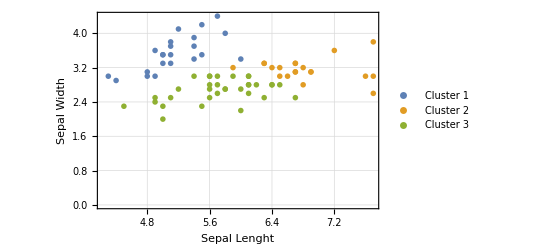

```mathematica
ListPlot[Pick[TsT,CC[TsT],#]&/@{1,2,3},PlotMarkers->"OpenMarkers",GridLines->Automatic,PlotLegends->{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]]},Frame->True,FrameTicks->All,FrameLabel->{"Sepal Lenght","Sepal Width"}]
```

```mathematica
31
```

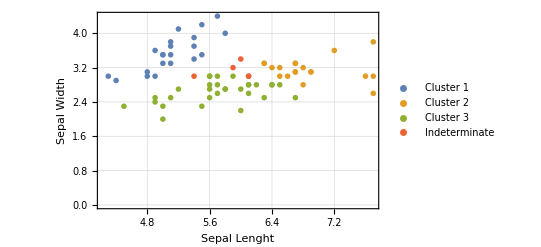

```mathematica
ListPlot[Pick[TsT,CC[TsT,IndeterminateThreshold-> 0.6],#]&/@{1,2,3,Indeterminate},PlotMarkers-> "OpenMarkers",PlotLegends->{Placeholder[Style["Cluster 1",Bold,Black,10]],Placeholder[Style["Cluster 2",Bold,Black,10]],Placeholder[Style["Cluster 3",Bold,Black,10]],Placeholder[Style["Indeterminate",Bold,Black,10]]},Frame->True,FrameTicks->All,FrameLabel->{"Sepal Lenght","Sepal Width"},GridLines->Automatic]
```